```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

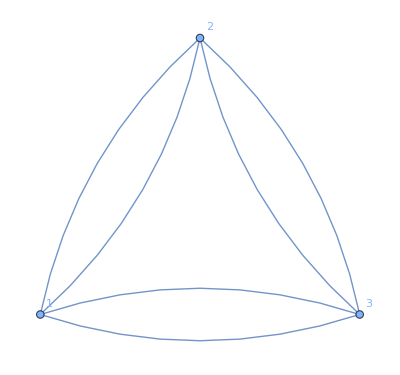

```mathematica
GraphPlot[{"1"->"2","2"->"3","3"->"1","1"->"3","2"->"1","3"->"2"},VertexLabels->Automatic]  (*3 pieces* Note that the graph remains the same after adding the TutteEmbedding Layout)
```

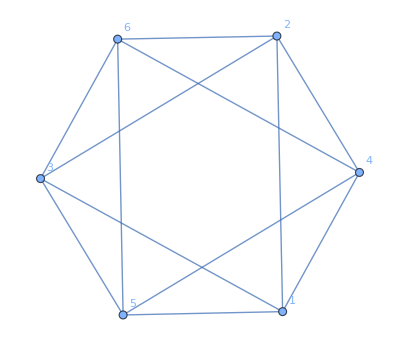

```mathematica
GraphPlot[{"1"->"2","1"->"5","2"->"4","2"->"3","3"->"6","3"->"1","4"->"6","4"->"1","5"->"3","5"->"4","6"->"2","6"->"5"},VertexLabels->Automatic] (*6 pieces*)
```

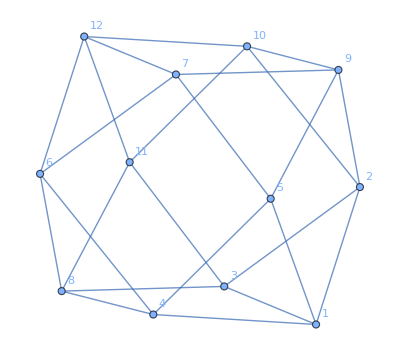

```mathematica
GraphPlot[{"1"->"3","1"->"5","2"->"1","2"->"10","3"->"2","3"->"8","4"->"1","4"->"6","5"->"9","5"->"4","6"->"7","6"->"8","7"->"5","7"->"12","8"->"4","8"->"11","9"->"2","9"->"7","10"->"11","10"->"9","11"->"3","11"->"12","12"->"6","12"->"10"},VertexLabels->Automatic] (*12 pieces*)
```

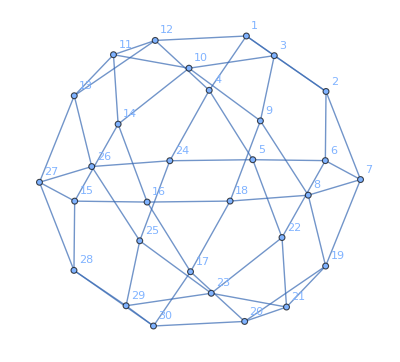

```mathematica
GraphPlot[{"1"->"3","1"->"4","2"->"1","2"->"7","3"->"2","3"->"10","4"->"12","4"->"5","5"->"24","5"->"6","6"->"2","6"->"22","7"->"6","7"->"8","8"->"9","8"->"19","9"->"3","9"->"18","10"->"11","10"->"9","11"->"12","11"->"14","12"->"13","12"->"1","13"->"26","13"->"11","14"->"15","14"->"10","15"->"16","15"->"27","16"->"14","16"->"17","17"->"18","17"->"30","18"->"8","18"->"16","19"->"7","19"->"20","20"->"21","20"->"17","21"->"19","21"->"23","22"->"5","22"->"21","23"->"22","23"->"29","24"->"25","24"->"4","25"->"26","25"->"23","26"->"24","26"->"27","27"->"13","27"->"28","28"->"29","28"->"15","29"->"30","29"->"25","30"->"28","30"->"20"},VertexLabels->Automatic] (*30 pieces*)
```

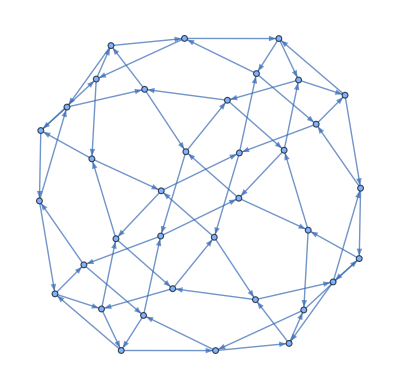

```mathematica
Graph[{"1"->"36","1"->"34","2"->"4","2"->"9","3"->"2","3"->"6","4"->"3","4"->"8","5"->"3","5"->"12","6"->"5","6"->"7","7"->"22","7"->"4","8"->"20","8"->"7","9"->"10","9"->"13","10"->"2","10"->"16","11"->"14","11"->"5","12"->"11","12"->"24","13"->"11","13"->"15","14"->"13","14"->"25","15"->"9","15"->"17","16"->"15","16"->"19","17"->"16","17"->"27","18"->"17","18"->"29","19"->"31","19"->"10","20"->"19","20"->"21","21"->"32","21"->"8","22"->"34","22"->"6","23"->"22","23"->"35","24"->"23","24"->"25","25"->"12","25"->"26","26"->"14","26"->"28","27"->"26","27"->"18","28"->"27","28"->"36","29"->"28","29"->"30","30"->"18","30"->"32","31"->"30","31"->"20","32"->"31","32"->"33","33"->"21","33"->"1","34"->"33","34"->"23","35"->"24","35"->"1","36"->"35","36"->"29"}] (*36pcs*)
```

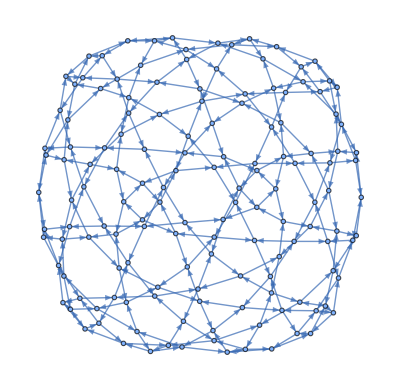

```mathematica
Graph[{"1"->"5","1"->"9","2"->"98","2"->"144","3"->"1","3"->"8","4"->"3","4"->"7","5"->"4","5"->"6","6"->"1","6"->"20","7"->"5","7"->"14","8"->"4","8"->"16","9"->"3","9"->"18","10"->"6","10"->"27","11"->"9","11"->"25","12"->"8","12"->"23","13"->"7","13"->"29","14"->"15","14"->"13","15"->"12","15"->"22","16"->"17","16"->"12","17"->"11","17"->"24","18"->"19","18"->"11","19"->"26","19"->"10","20"->"21","20"->"10","21"->"13","21"->"28","22"->"14","22"->"35","23"->"15","23"->"38","24"->"16","24"->"49","25"->"17","25"->"51","26"->"18","26"->"53","27"->"19","27"->"55","28"->"20","28"->"57","29"->"21","29"->"31","30"->"22","30"->"34","31"->"30","31"->"32","32"->"29","32"->"59","33"->"28","33"->"56","34"->"31","34"->"43","35"->"30","35"->"39","36"->"48","36"->"24","37"->"23","37"->"40","38"->"37","38"->"36","39"->"37","39"->"41","40"->"39","40"->"64","41"->"35","41"->"47","42"->"41","42"->"46","43"->"42","43"->"44","44"->"34","44"->"45","45"->"60","45"->"46","46"->"43","46"->"61","47"->"42","47"->"67","48"->"38","48"->"65","49"->"36","49"->"110","50"->"25","50"->"111","51"->"50","51"->"52","52"->"112","52"->"26","53"->"52","53"->"80","54"->"81","54"->"27","55"->"54","55"->"33","56"->"55","56"->"76","57"->"33","57"->"58","58"->"32","58"->"74","59"->"58","59"->"60","60"->"70","60"->"44","61"->"45","61"->"62","62"->"69","62"->"68","63"->"48","63"->"105","64"->"63","64"->"66","65"->"63","65"->"108","66"->"40","66"->"102","67"->"66","67"->"68","68"->"47","68"->"99","69"->"61","69"->"96","70"->"59","70"->"95","71"->"70","71"->"73","72"->"71","72"->"75","73"->"72","73"->"94","74"->"57","74"->"72","75"->"74","75"->"77","76"->"75","76"->"78","77"->"76","77"->"84","78"->"56","78"->"83","79"->"78","79"->"82","80"->"54","80"->"90","81"->"80","81"->"79","82"->"81","82"->"87","83"->"79","83"->"77","84"->"83","84"->"85","85"->"86","85"->"73","86"->"84","86"->"93","87"->"86","87"->"88","88"->"82","88"->"92","89"->"88","89"->"91","90"->"53","90"->"89","91"->"90","91"->"118","92"->"89","92"->"131","93"->"87","93"->"135","94"->"85","94"->"97","95"->"71","95"->"69","96"->"95","96"->"98","97"->"96","97"->"136","98"->"97","98"->"100","99"->"62","99"->"101","100"->"99","100"->"2","101"->"100","101"->"103","102"->"67","102"->"104","103"->"102","103"->"142","104"->"106","104"->"103","105"->"107","105"->"64","106"->"105","106"->"126","107"->"65","107"->"106","108"->"109","108"->"107","109"->"49","109"->"124","110"->"50","110"->"109","111"->"110","111"->"115","112"->"51","112"->"113","113"->"114","113"->"91","114"->"112","114"->"117","115"->"114","115"->"116","116"->"111","116"->"122","117"->"115","117"->"118","118"->"113","118"->"119","119"->"117","119"->"120","120"->"121","120"->"92","121"->"119","121"->"128","122"->"121","122"->"123","123"->"116","123"->"125","124"->"123","124"->"108","125"->"124","125"->"127","126"->"125","126"->"104","127"->"126","127"->"129","128"->"130","128"->"122","129"->"128","129"->"141","130"->"129","130"->"133","131"->"120","131"->"132","132"->"133","132"->"93","133"->"131","133"->"134","134"->"130","134"->"138","135"->"132","135"->"136","136"->"94","136"->"137","137"->"135","137"->"143","138"->"137","138"->"139","139"->"134","139"->"144","140"->"142","140"->"139","141"->"140","141"->"127","142"->"141","142"->"101","143"->"2","143"->"138","144"->"143","144"->"140"}] (*144pcs*)
```

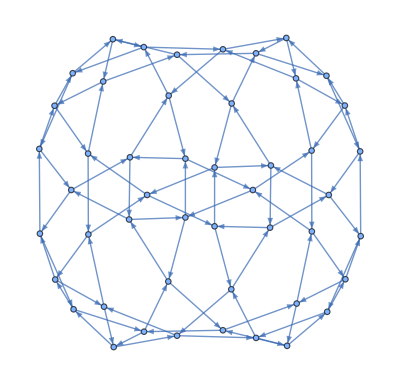

```mathematica
Graph[{"1"->"36","1"->"2","2"->"3","2"->"37","3"->"4","3"->"40","4"->"33","4"->"1","5"->"31","5"->"6","6"->"7","6"->"41","7"->"8","7"->"43","8"->"5","8"->"30","9"->"10","9"->"39","10"->"11","10"->"48","11"->"12","11"->"45","12"->"9","12"->"42","13"->"29","13"->"14","14"->"44","14"->"15","15"->"46","15"->"16","16"->"13","16"->"25","17"->"26","17"->"18","18"->"47","18"->"19","19"->"38","19"->"20","20"->"35","20"->"17","21"->"28","21"->"22","22"->"27","22"->"23","23"->"34","23"->"24","24"->"32","24"->"21","25"->"27","25"->"15","26"->"20","26"->"25","27"->"21","27"->"26","28"->"24","28"->"29","29"->"16","29"->"30","30"->"28","30"->"7","31"->"8","31"->"33","32"->"31","32"->"23","33"->"32","33"->"3","34"->"22","34"->"36","35"->"34","35"->"19","36"->"35","36"->"4","37"->"39","37"->"1","38"->"18","38"->"37","39"->"38","39"->"12","40"->"2","40"->"41","41"->"42","41"->"5","42"->"40","42"->"11","43"->"6","43"->"44","44"->"45","44"->"13","45"->"43","45"->"10","46"->"14","46"->"47","47"->"48","47"->"17","48"->"46","48"->"9"}] (*48 pieces*)
```

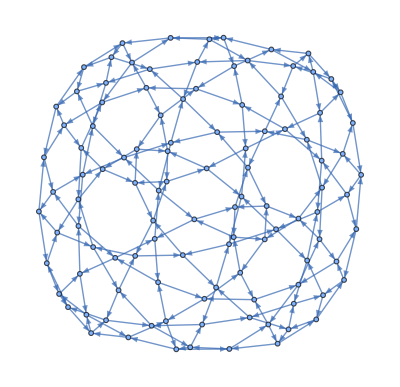

```mathematica
Graph[{"1"->"2","1"->"33","2"->"3","2"->"36","3"->"35","3"->"4","4"->"1","4"->"34","5"->"6","5"->"29","6"->"32","6"->"7","7"->"31","7"->"8","8"->"5","8"->"30","9"->"10","9"->"25","10"->"26","10"->"11","11"->"27","11"->"12","12"->"28","12"->"9","13"->"14","13"->"37","14"->"40","14"->"15","15"->"39","15"->"16","16"->"38","16"->"13","17"->"47","17"->"18","18"->"48","18"->"19","19"->"45","19"->"20","20"->"46","20"->"17","21"->"22","21"->"44","22"->"23","22"->"41","23"->"24","23"->"42","24"->"43","24"->"21","25"->"12","25"->"87","26"->"9","26"->"90","27"->"10","27"->"99","28"->"11","28"->"63","29"->"102","29"->"8","30"->"68","30"->"7","31"->"6","31"->"72","32"->"5","32"->"104","33"->"71","33"->"4","34"->"53","34"->"3","35"->"79","35"->"2","36"->"74","36"->"1","37"->"16","37"->"84","38"->"15","38"->"58","39"->"14","39"->"88","40"->"13","40"->"81","41"->"55","41"->"21","42"->"22","42"->"60","43"->"23","43"->"65","44"->"24","44"->"50","45"->"93","45"->"18","46"->"19","46"->"105","47"->"77","47"->"20","48"->"17","48"->"96","49"->"44","49"->"68","50"->"52","50"->"49","51"->"50","51"->"33","52"->"54","52"->"51","53"->"52","53"->"83","54"->"53","54"->"41","55"->"54","55"->"57","56"->"55","56"->"37","57"->"56","57"->"59","58"->"57","58"->"85","59"->"58","59"->"42","60"->"59","60"->"62","61"->"60","61"->"25","62"->"61","62"->"64","63"->"62","63"->"103","64"->"63","64"->"43","65"->"64","65"->"67","66"->"65","66"->"29","67"->"66","67"->"49","68"->"67","68"->"69","69"->"30","69"->"71","70"->"69","70"->"73","71"->"70","71"->"51","72"->"70","72"->"97","73"->"72","73"->"36","74"->"73","74"->"76","75"->"74","75"->"48","76"->"75","76"->"78","77"->"76","77"->"106","78"->"35","78"->"77","79"->"82","79"->"78","80"->"40","80"->"79","81"->"80","81"->"107","82"->"80","82"->"83","83"->"84","83"->"34","84"->"56","84"->"82","85"->"38","85"->"87","86"->"85","86"->"89","87"->"86","87"->"61","88"->"86","88"->"108","89"->"88","89"->"26","90"->"89","90"->"92","91"->"90","91"->"46","92"->"91","92"->"98","93"->"92","93"->"94","94"->"104","94"->"45","95"->"94","95"->"97","96"->"95","96"->"75","97"->"96","97"->"31","98"->"27","98"->"93","99"->"98","99"->"101","100"->"99","100"->"32","101"->"100","101"->"103","102"->"101","102"->"66","103"->"102","103"->"28","104"->"100","104"->"95","105"->"91","105"->"107","106"->"81","106"->"47","107"->"106","107"->"108","108"->"39","108"->"105"}] (*108pcs*)
```

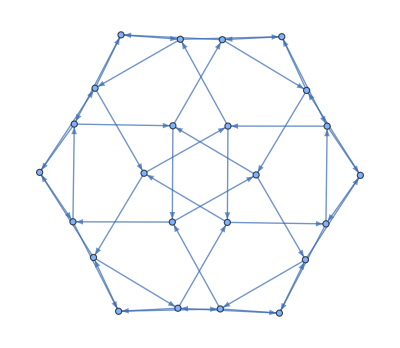

```mathematica
Graph[{"1"->"6","1"->"3","2"->"1","2"->"10","3"->"2","3"->"23","4"->"6","4"->"9","5"->"4","5"->"2","6"->"5","6"->"20","7"->"8","7"->"5","8"->"9","8"->"12","9"->"7","9"->"17","10"->"11","10"->"7","11"->"12","11"->"3","12"->"10","12"->"15","13"->"14","13"->"11","14"->"15","14"->"22","15"->"13","15"->"16","16"->"18","16"->"8","17"->"16","17"->"19","18"->"17","18"->"14","19"->"21","19"->"4","20"->"19","20"->"24","21"->"20","21"->"18","22"->"23","22"->"21","23"->"24","23"->"13","24"->"22","24"->"1"}]
(*24pcs*)
```

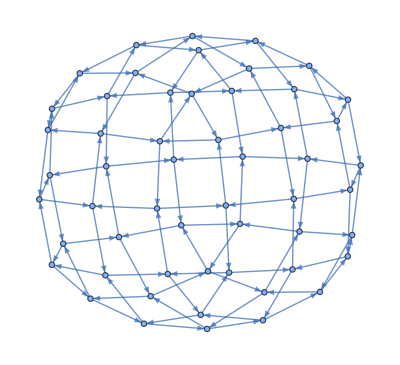

```mathematica
Graph[{"1"->"15","1"->"6","2"->"1","2"->"48","3"->"8","3"->"1","4"->"3","4"->"47","5"->"3","5"->"12","6"->"5","6"->"43","7"->"5","7"->"40","8"->"7","8"->"39","9"->"8","9"->"46","10"->"41","10"->"7","11"->"45","11"->"10","12"->"10","12"->"13","13"->"42","13"->"6","14"->"49","14"->"13","15"->"4","15"->"2","16"->"12","16"->"44","17"->"42","17"->"50","18"->"44","18"->"29","19"->"32","19"->"50","20"->"54","20"->"32","21"->"15","21"->"54","22"->"36","22"->"29","23"->"47","23"->"36","24"->"51","24"->"41","25"->"33","25"->"51","26"->"35","26"->"28","27"->"39","27"->"53","28"->"19","28"->"49","29"->"19","29"->"25","30"->"25","30"->"45","31"->"26","31"->"43","32"->"26","32"->"22","33"->"22","33"->"52","34"->"52","34"->"40","35"->"20","35"->"48","36"->"20","36"->"38","37"->"38","37"->"46","38"->"53","38"->"33","39"->"4","39"->"9","40"->"9","40"->"11","41"->"11","41"->"16","42"->"16","42"->"14","43"->"14","43"->"2","44"->"17","44"->"24","45"->"24","45"->"34","46"->"34","46"->"27","47"->"27","47"->"21","48"->"21","48"->"31","49"->"31","49"->"17","50"->"28","50"->"18","51"->"18","51"->"30","52"->"30","52"->"37","53"->"37","53"->"23","54"->"23","54"->"35"}] (*54pcs*)
```

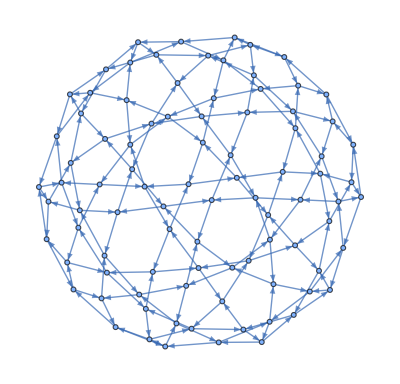

```mathematica
Graph[{"1"->"5","1"->"3","2"->"1","2"->"44","3"->"2","3"->"9","4"->"1","4"->"7","5"->"4","5"->"22","6"->"4","6"->"16","7"->"6","7"->"23","8"->"6","8"->"13","9"->"8","9"->"10","10"->"3","10"->"40","11"->"10","11"->"43","12"->"2","12"->"46","13"->"9","13"->"15","14"->"13","14"->"38","15"->"17","15"->"14","16"->"19","16"->"8","17"->"16","17"->"18","18"->"34","18"->"15","19"->"26","19"->"17","20"->"14","20"->"41","21"->"5","21"->"24","22"->"21","22"->"45","23"->"21","23"->"25","24"->"23","24"->"90","25"->"7","25"->"29","26"->"25","26"->"27","27"->"19","27"->"32","28"->"27","28"->"63","29"->"31","29"->"26","30"->"29","30"->"33","31"->"30","31"->"89","32"->"30","32"->"28","33"->"80","33"->"32","34"->"28","34"->"35","35"->"18","35"->"37","36"->"39","36"->"35","37"->"36","37"->"62","38"->"36","38"->"20","39"->"38","39"->"58","40"->"20","40"->"11","41"->"40","41"->"42","42"->"52","42"->"39","43"->"51","43"->"44","44"->"11","44"->"12","45"->"12","45"->"87","46"->"45","46"->"48","47"->"46","47"->"73","48"->"47","48"->"49","49"->"50","49"->"43","50"->"48","50"->"54","51"->"49","51"->"52","52"->"53","52"->"41","53"->"51","53"->"55","54"->"53","54"->"71","55"->"54","55"->"57","56"->"55","56"->"68","57"->"56","57"->"58","58"->"42","58"->"59","59"->"57","59"->"61","60"->"59","60"->"66","61"->"60","61"->"37","62"->"61","62"->"63","63"->"64","63"->"34","64"->"62","64"->"79","65"->"64","65"->"67","66"->"65","66"->"68","67"->"66","67"->"78","68"->"60","68"->"69","69"->"76","69"->"56","70"->"69","70"->"72","71"->"70","71"->"50","72"->"71","72"->"75","73"->"72","73"->"74","74"->"47","74"->"86","75"->"83","75"->"73","76"->"70","76"->"77","77"->"83","77"->"67","78"->"77","78"->"80","79"->"65","79"->"33","80"->"79","80"->"81","81"->"78","81"->"88","82"->"81","82"->"85","83"->"76","83"->"84","84"->"82","84"->"75","85"->"84","85"->"90","86"->"85","86"->"87","87"->"74","87"->"22","88"->"31","88"->"82","89"->"88","89"->"24","90"->"89","90"->"86"}] (*90 pieces*)
```

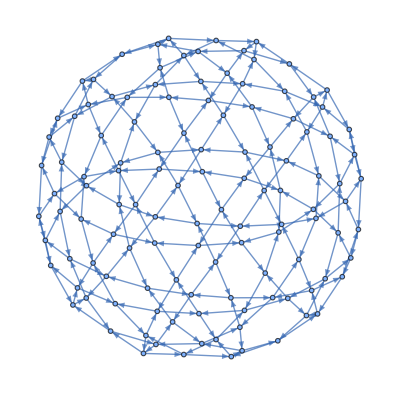

```mathematica
Graph[{"1"->"7","1"->"3","2"->"1","2"->"5","3"->"2","3"->"9","4"->"2","4"->"21","5"->"4","5"->"16","6"->"1","6"->"11","7"->"6","7"->"22","8"->"17","8"->"3","9"->"8","9"->"10","10"->"14","10"->"6","11"->"10","11"->"13","12"->"11","12"->"45","13"->"12","13"->"36","14"->"42","14"->"9","15"->"8","15"->"18","16"->"15","16"->"19","17"->"15","17"->"46","18"->"91","18"->"16","19"->"5","19"->"26","20"->"4","20"->"23","21"->"20","21"->"27","22"->"20","22"->"24","23"->"22","23"->"30","24"->"7","24"->"35","25"->"28","25"->"19","26"->"25","26"->"70","27"->"25","27"->"29","28"->"27","28"->"69","29"->"21","29"->"31","30"->"29","30"->"32","31"->"30","31"->"66","32"->"23","32"->"34","33"->"32","33"->"37","34"->"33","34"->"63","35"->"33","35"->"36","36"->"24","36"->"39","37"->"59","37"->"35","38"->"37","38"->"40","39"->"38","39"->"13","40"->"39","40"->"56","41"->"14","41"->"48","42"->"44","42"->"41","43"->"42","43"->"52","44"->"43","44"->"12","45"->"44","45"->"55","46"->"41","46"->"47","47"->"17","47"->"89","48"->"46","48"->"50","49"->"48","49"->"93","50"->"49","50"->"51","51"->"87","51"->"43","52"->"51","52"->"54","53"->"52","53"->"84","54"->"53","54"->"45","55"->"54","55"->"40","56"->"58","56"->"55","57"->"56","57"->"83","58"->"57","58"->"60","59"->"61","59"->"38","60"->"59","60"->"81","61"->"60","61"->"62","62"->"78","62"->"34","63"->"62","63"->"65","64"->"63","64"->"76","65"->"64","65"->"31","66"->"65","66"->"68","67"->"66","67"->"74","68"->"67","68"->"28","69"->"68","69"->"72","70"->"71","70"->"18","71"->"99","71"->"26","72"->"71","72"->"73","73"->"69","73"->"102","74"->"73","74"->"75","75"->"67","75"->"105","76"->"75","76"->"77","77"->"64","77"->"79","78"->"77","78"->"61","79"->"78","79"->"107","80"->"79","80"->"82","81"->"80","81"->"58","82"->"81","82"->"109","83"->"82","83"->"84","84"->"57","84"->"85","85"->"53","85"->"94","86"->"85","86"->"88","87"->"50","87"->"86","88"->"87","88"->"117","89"->"49","89"->"90","90"->"47","90"->"92","91"->"90","91"->"70","92"->"91","92"->"97","93"->"89","93"->"95","94"->"86","94"->"110","95"->"88","95"->"96","96"->"93","96"->"118","97"->"96","97"->"98","98"->"92","98"->"100","99"->"98","99"->"72","100"->"99","100"->"120","101"->"100","101"->"103","102"->"101","102"->"74","103"->"102","103"->"114","104"->"103","104"->"106","105"->"104","105"->"76","106"->"105","106"->"108","107"->"106","107"->"80","108"->"107","108"->"113","109"->"112","109"->"83","110"->"111","110"->"109","111"->"94","111"->"116","112"->"110","112"->"108","113"->"112","113"->"114","114"->"115","114"->"104","115"->"113","115"->"119","116"->"115","116"->"117","117"->"111","117"->"95","118"->"97","118"->"119","119"->"120","119"->"116","120"->"118","120"->"101"}] (*120 pieces*)
```